```mathematica
m1Y00=-0.396743
m1Y01=-0.511481
m1Y02=-0.32191
m1Y03=0.013108
m1Y04=0.303736
m1Y05=0.421366
m1Y06=0.321412
m1Y07=0.110209
m1Y08=-0.100258
m1Y09=-0.202904
m1Y010=-0.170356
m1Y011=-0.103884
m1Y012=-0.0194434
NConst =1.00
m1[θ_]=m1Y00*SphericalHarmonicY[0,0,θ,0]+m1Y01*SphericalHarmonicY[1,0,θ,0]+m1Y02*SphericalHarmonicY[2,0,θ,0]+m1Y03*SphericalHarmonicY[3,0,θ,0]+m1Y04*SphericalHarmonicY[4,0,θ,0]+m1Y05*SphericalHarmonicY[5,0,θ,0]+m1Y06*SphericalHarmonicY[6,0,θ,0]+m1Y07*SphericalHarmonicY[7,0,θ,0]+m1Y08*SphericalHarmonicY[8,0,θ,0]+m1Y09*SphericalHarmonicY[9,0,θ,0]+
m1Y010*SphericalHarmonicY[10,0,θ,0]+m1Y011*SphericalHarmonicY[11,0,θ,0]+m1Y012*SphericalHarmonicY[12,0,θ,0]

SphericalPlot3D[{((1/NConst)*m1[θ])^2, (3/(4 Pi))^(2/3)},{θ,0,π},{ϕ,0,π}, PlotRange -> All]
Plot[{((1/NConst)*m1[θ])^2, (3/(4 Pi))^(2/3)},{θ,0,π}, PlotRange -> All]
```

-0.396743

-0.511481

-0.32191

0.013108

0.303736

0.421366

0.321412

0.110209

-0.100258

-0.202904

-0.170356

-0.103884

-0.0194434

1.

-0.111919-0.249911 Cos[θ]-0.101528 (-1+3 Cos[θ]^2)+0.0048916 (-3 Cos[θ]+5 Cos[θ]^3)+0.0321309 (3-30 Cos[θ]^2+35 Cos[θ]^4)+0.0492789 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)+0.0204319 (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)+0.00752554 (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7)-0.000911021 (35-1260 Cos[θ]^2+6930 Cos[θ]^4-12012 Cos[θ]^6+6435 Cos[θ]^8)-0.00194918 (315 Cos[θ]-4620 Cos[θ]^3+18018 Cos[θ]^5-25740 Cos[θ]^7+12155 Cos[θ]^9)-0.000860245 (-63+3465 Cos[θ]^2-30030 Cos[θ]^4+90090 Cos[θ]^6-109395 Cos[θ]^8+46189 Cos[θ]^10)-0.000548994 (-693 Cos[θ]+15015 Cos[θ]^3-90090 Cos[θ]^5+218790 Cos[θ]^7-230945 Cos[θ]^9+88179 Cos[θ]^11)-0.0000267816 (231-18018 Cos[θ]^2+225225 Cos[θ]^4-1021020 Cos[θ]^6+2078505 Cos[θ]^8-1939938 Cos[θ]^10+676039 Cos[θ]^12)

-Graphics3D-

```mathematica
Export["D:\\Documents\\College\\OSU\\Research\\Sph. Harmonics proj\\SphHarEvol.1.cpp\\SphHarEvol.1.1\\45-40-300 with 100 species.jpg",%389,"JPEG"]
```

D:\Documents\College\OSU\Research\Sph. Harmonics proj\SphHarEvol.1.cpp\SphHarEvol.1.1\45-40-300 with 100 species.jpg

```mathematica
Export["D:\\Documents\\College\\OSU\\Research\\Sph. Harmonics proj\\SphHarEvol.1.cpp\\SphHarEvol.1.1\\90-20-200 with 100 species.jpg",%370,"JPEG"]
```

D:\Documents\College\OSU\Research\Sph. Harmonics proj\SphHarEvol.1.cpp\SphHarEvol.1.1\90-20-200 with 100 species.jpg

```mathematica
Simplify[NConst]
```

1.

```mathematica
N[Integrate[Sin[θ](m1[θ]/NConst)^2 , {θ,0,Pi},{ϕ,0,2 Pi}]]
```

0.999485

```mathematica
N[Sqrt[11848.519319371622]]
```

108.851

```mathematica
Show[%724,ViewPoint->{0,-∞,0}]
```

```mathematica
SphericalPlot3D[{ (1/NConst)*SphericalHarmonicY[0,0,θ,ϕ]+(2/NConst)*SphericalHarmonicY[1,0,θ,ϕ] , (3/(4 Pi))^(1/3) },{θ,0,Pi},{ϕ,0,Pi}, PlotRange -> All]
```

-Graphics3D-

```mathematica
SphericalPlot3D[{ (2/NConst)*SphericalHarmonicY[1,0,θ,ϕ] , (3/(4 Pi))^(1/3) },{θ,0,Pi},{ϕ,0,Pi/2}, PlotRange -> All]
```

-Graphics3D-

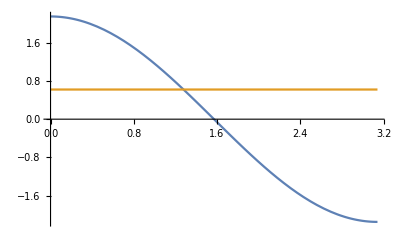

1.

```mathematica
Plot[{(2/NConst)*SphericalHarmonicY[1,0,θ,0] , (3/(4 Pi))^(1/3) },{θ,0,Pi}, PlotRange -> All]
```

```mathematica
N[m1[π/1.001]^2 * Sin[π/1.001]]
```

0.000382591